```mathematica
samplingList={10,20,50};
samplingList=Table[
samplingList*10^ii
,{ii,0,5}]//Flatten;
PiList=Table[
Print["Total number of sampling: ",NumberOfSample];
Print["Job done in ",
Timing[
xSample=RandomReal[{0,1},NumberOfSample];
ySample=RandomReal[{0,1},NumberOfSample];
pointPool=Partition[Riffle[xSample,ySample],2];
circles=Select[pointPool,#[[1]]^2+#[[2]]^2≤1&];
ValueOfPi=N@Length@circles*4/NumberOfSample;
][[1]]
,"s; ", "Estimate of π: ",ValueOfPi];
ValueOfPi
,{NumberOfSample,samplingList}];
```

Total number of sampling: 10

Job done in 0.005804s; Estimate of π: 3.2

Total number of sampling: 20

Job done in 0.00015s; Estimate of π: 3.2

Total number of sampling: 50

Job done in 0.000119s; Estimate of π: 3.52

Total number of sampling: 100

Job done in 0.000206s; Estimate of π: 3.04

Total number of sampling: 200

Job done in 0.000382s; Estimate of π: 3.

Total number of sampling: 500

Job done in 0.000917s; Estimate of π: 3.16

Total number of sampling: 1000

Job done in 0.001994s; Estimate of π: 3.024

Total number of sampling: 2000

Job done in 0.003876s; Estimate of π: 3.218

Total number of sampling: 5000

Job done in 0.064916s; Estimate of π: 3.1152

Total number of sampling: 10000

Job done in 0.123007s; Estimate of π: 3.1552

Total number of sampling: 20000

Job done in 0.263566s; Estimate of π: 3.1254

Total number of sampling: 50000

Job done in 0.620111s; Estimate of π: 3.14688

Total number of sampling: 100000

Job done in 1.16385s; Estimate of π: 3.13436

Total number of sampling: 200000

Job done in 1.3444s; Estimate of π: 3.13782

Total number of sampling: 500000

Job done in 1.91211s; Estimate of π: 3.13683

Total number of sampling: 1000000

Job done in 2.87822s; Estimate of π: 3.13938

Total number of sampling: 2000000

Job done in 4.82213s; Estimate of π: 3.1429

Total number of sampling: 5000000

Job done in 11.1829s; Estimate of π: 3.14207

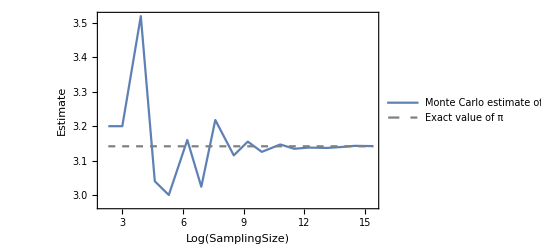

```mathematica
Show[ListPlot[
Partition[
Riffle[Log@samplingList,PiList]
,2]
,PlotLegends->{"Monte Carlo estimate of π"},Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"Estimate",None},{"Log(SamplingSize)",None}}],
Plot[Pi,{x,Min@Log@samplingList,Max@Log@samplingList}
,PlotStyle->{Dashed,Gray},PlotLegends->{"Exact value of π"}]
]
```